## From data to distribution

Last week we saw a lot of ways you can make predictions in Mathematica when you know the distribution of a given random variable. However, a lot of the time we won’t necessarily know the exact distribution. As such, this section lists a bunch of ways you can get a usable distribution in Mathematica from data.

### EstimatedDistribution

Let’s say we know the form a distribution should take. For instance, some examples: 

	If it’s a distribution of sample means we likely know it’s normally distributed or t-distributed.

	If it’s a distribution of sample variances it will likely be chi-squared distributed. 

	If your data reflects the amount of time for an event with fixed probabiity will take to occur it will likely follow an Erlang 
	distribution. 
	
	If your data reflects the expected number of fixed probability events that will occur in a given amount of time, it will likely follow a 
	Poisson distribution.
	
There are a lot more examples, and if you take a course like prob-stat you’ll be introduced to many of them. However, knowing what distribution your variable is expected to follow is only half of the battle. Once we’ve identified the distribution our data should follow, we still need to know what parameters of that distribution actually fit our data. For a normal distribution this would be the mean and standard deviation of the distribution for example. And this is the part Mathematica can do very well for us using the EstimatedDistribution function.

So let’s say we have the following data we know should be normally distributed, and let’s find the best possible mean and variance which fit that data

```mathematica
data={4.100470330941686,4.803962516720279,3.9722423770934974,3.8821625860370745,4.144065579525581,4.100466054232558,3.858372275486983,4.666148739989296,4.343988081700685,4.191628558184307,4.131642158145729,4.129592075714686,3.969808230602357,3.587919042500251,3.6130547358979563,4.065949112903856,3.883885287584382,4.000686291538765,4.108894915763135,4.115133344284764,3.777414794247984,3.8646737208262234,4.3799884805454985,4.303309106733864,3.9307908380640213,3.9654992392970727,3.5629961149329366,3.617712784330881,3.376520050076799,3.9927336661200146,4.043986603828804,3.7692258394313565,3.892697491309486,4.27769867102704};
```

```mathematica
FitDist=EstimatedDistribution[data,NormalDistribution[μ,σ]]
```

NormalDistribution[4.01251,0.291697]

So we can see that we’ve gone from the data to a distribution we can use in Mathematica. But first let’s visually see how well this reflects the data with yet another Histogram

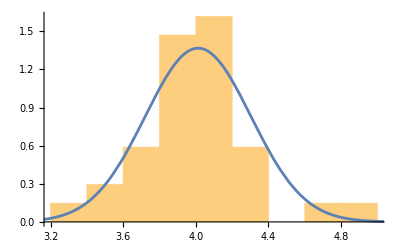

```mathematica
Show[{
Histogram[data,Automatic,"PDF"],
Plot[PDF[FitDist,x],{x,-1,8},PlotRange->All]
}]
```

From this it seems the data fits pretty well, and so we could use this distribution to do anything we learned how to do last week, like using it with (N)Probability or (N)Expectation

```mathematica
NProbability[16<x^2,x\[Distributed]FitDist]
NExpectation[Cos[x/10],x\[Distributed]FitDist]
```

0.517103

0.920182

However, you may be thinking, why can’t I just use the mean and standard deviation to do this manually? And you absolutely can, so let’s do that and compare the result to the one Mathematica gives

```mathematica
FitDist=EstimatedDistribution[data,NormalDistribution[μ,σ]]
ManuallyFitDist=NormalDistribution[Mean[data],StandardDeviation[data]*√((Length[data]-1)/Length[data])]
```

NormalDistribution[4.01251,0.291697]

NormalDistribution[4.01251,0.291697]

NOTE: The EstimatedDistribution results provide potentially biased distribution parameters, which is why we needed to undo the Bessel (i.e. why we multiply the sample standard deviation by √((n-1)/n)in the above manually fit example). With large enough sample sizes the parameter values will always still approach the values of the true distribution, but if you were to make a distribution of the parameter values for a given, finite sample size their mean will not always be the values of the true distribution parameters. 

Anyway, for something like a normal distribution, this process is easy enough to do by hand. But for more complicated distributions the parameters may not be as simple as the mean and standard deviation and so letting Mathematica do it for you can save a good deal of time. For instance let’s look at something like an Erlang distribution.

```mathematica
ErlangData = {2.62678866177761,5.572975512445796,7.3623164926257285,0.6998448636232828,1.8441114008548798,4.069745314687529,7.115740836890558,5.782751175964615,1.2858718652357468,3.5575291156265583,2.5396491515523376,2.47111190165203,3.863508894239784,4.038000531194897,3.6633110778417084,2.09501228388054,4.4315584730305,7.8627422445987305,6.4003929688210786,5.663333555500326,2.93485876156107,2.382058529620403,3.915748507962947,4.761022184581413,4.397373409794755,4.370790742384198,4.679848984061228,5.044701476741371,6.224801662087282,1.3066354282080157,8.892386435624795,2.6191687832304584,3.97929544565455};

Clear[k,λ];
FitDist=EstimatedDistribution[ErlangData,ErlangDistribution[k,λ]]
```

ErlangDistribution[4,0.953378]

Here the parameters aren’t just the mean and variance they’re what are known as the “shape” factor k, and the “rate” factor λ. And so finding them is less straight forward. Additionally, there are multiple methods you can use to predict these values from the data and by default Mathematica uses something known as Maximum likelihood estimation. In most cases this is a great option, but Mathematica also let’s you use other common methods which may give slightly different values for certain distributions.

```mathematica
EstimatedDistribution[ErlangData,ErlangDistribution[k,λ],ParameterEstimator->"MaximumLikelihood"]
EstimatedDistribution[ErlangData,ErlangDistribution[k,λ],ParameterEstimator->"MethodOfMoments"]
EstimatedDistribution[ErlangData,ErlangDistribution[k,λ],ParameterEstimator->"MethodOfCentralMoments"]
EstimatedDistribution[ErlangData,ErlangDistribution[k,λ],ParameterEstimator->"MethodOfCumulants"]
EstimatedDistribution[ErlangData,ErlangDistribution[k,λ],ParameterEstimator->"MethodOfFactorialMoments"]
```

ErlangDistribution[4,0.953378]

ErlangDistribution[4.45308,1.06137]

ErlangDistribution[4.45308,1.06137]

ErlangDistribution[4.45308,1.06137]

«1 more identical outputs»

Note that in the example we did by hand for the Normal distribution, we essentially used the Method Of Central Moments, which is different from Mathematica’s default Maximum Likelihood method.

### HistogramDistribution

Ok, but what if we only have data and have no idea what theoretical distribution the samples come from? In that case, one thing we could do is take the data to be the be-all and end-all of truth. In other words, we could treat the histogram as the distribution. Obviously this will result in a fairly blocky distribution. But it’s an okay-ish approximation if we have enough data and truly have no idea what distribution we’re playing with. 

To do this in Mathematica we can simply use the HistogramDistribution function:

```mathematica
(* First lets generate 50 points from an actual distribution *)
SeedRandom[0];
data = RandomVariate[ProbabilityDistribution[1/(2 Gamma[5/4])ⅇ^(-x^4),{x,-∞,∞}],50];
(* Now let's find the emperical fit *) 
dist=HistogramDistribution[data]
```

DataDistribution[…]

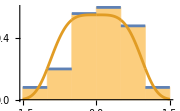
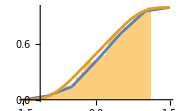

```mathematica
(* Now lets visulaize the resulting distribution's pdf and CDF *)
Row[{Show[{
Histogram[data,Automatic,"PDF"],
Plot[{PDF[dist,x],1/(2 Gamma[5/4])ⅇ^(-x^4)},{x,-1.5,1.5},PlotLegends->{"Histogram Distribution","True Distribution"},PlotPoints->500]
},ImageSize->Small],
Show[{
Histogram[data,50,"CDF"],
Plot[Evaluate[{CDF[dist,x],Integrate[{1/(2 Gamma[5/4])ⅇ^(-u^4)},{u,-∞,x},GenerateConditions->False][[1]]}],{x,-1.5,1.5},PlotLegends->{"Histogram Distribution","True Distribution"},PlotPoints->500]
},PlotRange->{{-1.5,1.5},Automatic},ImageSize->Small]}]
```

We can also use these DataDistributions in the same way as any other distribution in Mathematica:

```mathematica
NProbability[0.1<x^2,x\[Distributed]dist]
NExpectation[Cos[x],x\[Distributed]dist]
RandomVariate[dist]
CDF[dist]
```

0.633176

0.827288

0.151309

Function[{x$},CDF[DataDistribution[…],x$],{Listable}]

However, whenever you define a histogram, you have the options of defining how many bins you want. By default Mathematica will find a good number of bins for you, but you can change this if you want by passing a second value to the function like so:

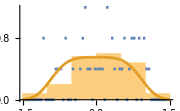
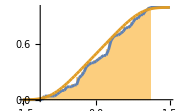

```mathematica
dist=HistogramDistribution[data,50];
Row[{Show[{
Histogram[data,Automatic,"PDF"],
Plot[{PDF[dist,x],1/(2 Gamma[5/4])ⅇ^(-x^4)},{x,-1.5,1.5},PlotLegends->{"Histogram Distribution","True Distribution"},PlotPoints->500]
},ImageSize->Small],
Show[{
Histogram[data,50,"CDF"],
Plot[Evaluate[{CDF[dist,x],Integrate[{1/(2 Gamma[5/4])ⅇ^(-u^4)},{u,-∞,x},GenerateConditions->False][[1]]}],{x,-1.5,1.5},PlotLegends->{"Histogram Distribution","True Distribution"},PlotPoints->500]
},PlotRange->{{-1.5,1.5},Automatic},ImageSize->Small]}]
```

However we can see that as we do this, we smooth the data less and so the resulting distribution perfectly matches the data, but it becomes a worse approximation of the true distribution.

### FindDistribution

Ok, so that seemed somewhat useful but not great, especially when we have small sample sizes... Is there any way we can do better? Well, not without making any assumptions, no. 

However, we could assume that the true distribution is a common distribution, and then we could try to use EstimatedDistribution against a list of common distributions and pick the one that fits the data the best. 

This would be a bit of a pain to do manually, so thankfully Mathematica has yet another built in function to do this known as FindDistribution. Essentially, FindDistribution will fit the data to all of the following distributions and find the one that works best: 
-Graphics-

Here’s how we can use it

ExponentialDistribution[1.08855]

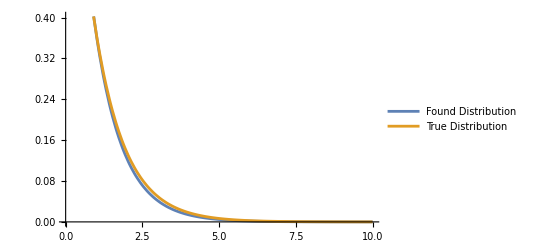

```mathematica
SeedRandom[1232123];
data=RandomVariate[ExponentialDistribution[1],100];
dist=FindDistribution[data]

Plot[{PDF[dist,x],PDF[ExponentialDistribution[1],x]},{x,0,10},PlotLegends->{"Found Distribution","True Distribution"}]
```

Woa! Using no information about the distribution type it was able to tell we sampled that data from an exponential distribution!

Additionally, if we want Mathematica to return a list of the top 10 distributions it found, for-instance, we could pass the function a second variable as follows:

```mathematica
dists=FindDistribution[data,10]
```

{ExponentialDistribution[1.08855],WeibullDistribution[0.977069,0.898369,0.0109258],GammaDistribution[0.922638,0.995685],WeibullDistribution[0.959429,0.902373],ParetoDistribution[7.,5.90698,1.31563,0.0109258],HalfNormalDistribution[0.982036],LogNormalDistribution[-0.71653,1.34287],ChiDistribution[0.937594],ChiSquareDistribution[0.918657],FrechetDistribution[1.71956,0.711001,-0.328364]}

And then we can see how well all these distributions look

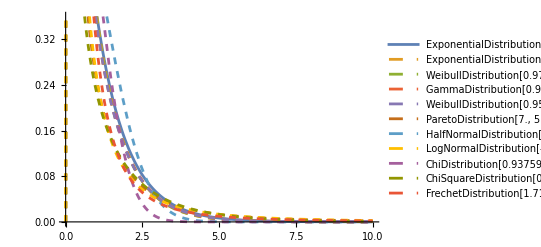

```mathematica
Plot[Evaluate[{PDF[ExponentialDistribution[1],x],Sequence@@(PDF[#,x]&/@dists)}],{x,0,10},PlotLegends->ToString/@{ExponentialDistribution[1],Sequence@@dists},PlotStyle->{Automatic,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed}]
```

However,  it actually gets more crazy than this. For really weird distributions, Mathematica will try to find a mixture of distributions which fit the data. For instance, if you had data being sampled from two independent populations but which your sampling process treated as a single variable, you might expect to get some form of bi-modal distribution. Let’s look at an example.

Say I go to a combined Dutch and Indonesian cultural event (hey, it could happen), and while I’m there I sample the heights of 1000 attendees. By pure chance I’ll get some people who are from the Netherlands, and the rest will be from Indonesia. However, people from the Netherlands are on average the tallest on earth with heights distributed by NormalDistribution[183, 9.7], while people from Indonesia have the shortest heights of all people having a distribution of NormalDistribution[158, 7.8]. 

If we simulate this sampling process we get the following data

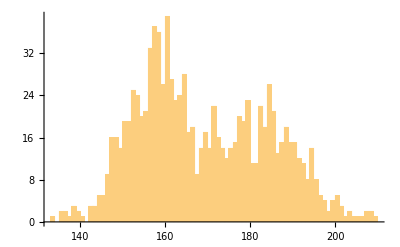

```mathematica
SeedRandom[50];
n=1000;
Netherlands=RandomInteger[{1,n}];
Indonesia=n-Netherlands;
data=Join[RandomVariate[NormalDistribution[183,9.7],Netherlands],RandomVariate[NormalDistribution[158,7.8],Indonesia]];
Histogram[data,100]
```

We can see that while the heights of each population are normally distributed, the distribution in our sample is far from normal looking, it is what’s known as a mixed distribution. Now here is the really crazy part. 

If we use FindDistribution Mathematica will figure this out for us even though this is a wack looking distribution

```mathematica
dist=FindDistribution[data]
```

MixtureDistribution[{0.592748,0.407252},{NormalDistribution[157.087,7.09003],NormalDistribution[181.551,10.2955]}]

And look at that! The distribution which results says it is a mix of two normal distribution which are really dang close to the two distributions we used to generate the data. And what’s more, the weights of each distribution in the mixed distribution are the ratio of Indonesian to Dutch people in the sample! That’s some pretty slick data analysis if you ask me!

```mathematica
Indonesia/n//N
Netherlands/n//N
```

0.555

0.445

Finally, let’s look at the fit:

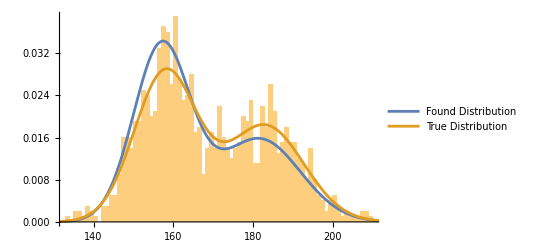

```mathematica
TrueDist=MixtureDistribution[{Indonesia/n,Netherlands/n},{NormalDistribution[158,7.8],NormalDistribution[183,9.7]}];
Show[{
Histogram[data,100,"PDF"],
Plot[{PDF[dist,x],PDF[TrueDist,x]},{x,120,220},PlotLegends->{"Found Distribution","True Distribution"}]
}]
```

We can see that it’s not perfect, it’s still pretty dang impressive. And if we had more data points it would get much closer to the true distribution.

## Hypothesis Testing

In this next section I want to show you how to use some of Mathematica’s built in Hypothesis Test functions. They all work in a similar way, so hopefully if I give some examples you’ll be able to use whichever ones you want. Let’s start with a simple distribution of sample means. If you’ve taken a stats class you know there are a few ways to do this and Mathematica has built in functions for all of them. But its most general function is called LocationTest which we’ll work with first:

### LocationTest

If we give location test two sets of data, it will perform one of several statistical tests on the data sets essentially asking the question “are the means of these data sets equal?” Let’s look at an example

```mathematica
SeedRandom[12372819];
data1=RandomVariate[NormalDistribution[4,1],500];
data2=RandomVariate[NormalDistribution[4,0.2],500];
LocationTest[{data1,data2}]
```

0.835779

By default Mathematica returns a p-value of the test, but in it’s own this isn’t very useful because we don’t know what test it actually used in the background, or necessarily what this even means unless we’re stats wizards ourselves. Instead, we need to ask Mathematica for more information about the result which we can do by passing the function a second parameter which can be any of the following: 
-Graphics-
So by default we’re essentially getting LocationTest[{data1, data2},Automatic,"PValue"]
The reason we need to pass Automatic as the second option, is due to another use case of the function which we’ll show in a little bit

```mathematica
LocationTest[{data1,data2},Automatic,"PValue"]
```

0.835779

However, some of these other options tend to be much more useful. For instance, perhaps one of the most useful to people who may not know the most about stats is the proper conclusion to draw from the test so we can ask Mathematica for “TestConclusion”

```mathematica
LocationTest[{data1,data2},Automatic,"TestConclusion"]
```

The null hypothesis that the mean difference is 0 is not rejected at the 5 percent level based on the T test.

And we can see it tells us in plain English what the test tells us about the data. And it also tells us that it used a sample T-Test and a confidence level of 95% (or type 1-error of 5%). We could also change this confidence level if we want as follows:

```mathematica
LocationTest[{data1,data2},Automatic,"TestConclusion",SignificanceLevel->0.01]
```

The null hypothesis that the mean difference is 0 is not rejected at the 1. percent level based on the T test.

So in other words, we do not have statistically significant data to conclude that these two sets of data come from distributions with different means. Which is what we’d expect considering we know they have the same mean in this case. 

Additionally, we can explore some of the other properties we can as Mathematica for. Another useful on is {“TestDataTable”, All} which will give a table of all possible tests and their results

```mathematica
LocationTest[{data1,data2},Automatic,{"TestDataTable",All},SignificanceLevel->0.01]
```

| Statistic | P-Value
Mann-Whitney | 122865. | 0.640049
Paired T | -0.205208 | 0.837493
Paired Z | -0.205208 | 0.83741
Sign | 240 | 0.395511
Signed-Rank | 61197. | 0.658755
T | -0.207396 | 0.835779
Z | -0.207396 | 0.835701

Or if we wanted a table of the conclusions of all the tests we could do something like this

```mathematica
LocationTest[{data1,data2},Automatic,{"TestConclusion",All},SignificanceLevel->0.01]//Column
```

The null hypothesis that the median difference is 0 is not rejected at the 1. percent level based on the Mann-Whitney test.
The null hypothesis that the mean difference is 0 is not rejected at the 1. percent level based on the Paired T test.
The null hypothesis that the mean difference is 0 is not rejected at the 1. percent level based on the Paired Z test.
The null hypothesis that the median difference is 0 is not rejected at the 1. percent level based on the Sign test.
The null hypothesis that the median difference is 0 is not rejected at the 1. percent level based on the Signed-Rank test.
The null hypothesis that the mean difference is 0 is not rejected at the 1. percent level based on the T test.
The null hypothesis that the mean difference is 0 is not rejected at the 1. percent level based on the Z test.

So we can see that all the tests give the same result. You have to be careful doing this though, because if some tests gave different results you could get into a situation where you accidentally bias your results. For instance, it would not be correct to just choose the test which gives you the most desirable p-value because then you would be  introducing bias. As such, it’s usually best to either just use the test Mathematica automatically chooses or to have a test in mind and tell Mathematic to use that one which we can do as follows: 

First if we want a list of available tests we can run

```mathematica
LocationTest[{data1,data2},Automatic,{"AllTests"}]
```

{{MannWhitney,PairedT,PairedZ,Sign,SignedRank,T,Z}}

And then we can ask for one of these in the properties list as follows

```mathematica
LocationTest[{data1,data2},Automatic,{"TestConclusion","Z"}]
```

The null hypothesis that the mean difference is 0 is not rejected at the 5 percent level based on the Z test.

Finally if we only have one data set we can also simply test if its mean by specifying that value in the spot we previously wrote “Automatic” in

```mathematica
LocationTest[data1,6,"TestConclusion",SignificanceLevel->0.01]
```

The null hypothesis that the mean of the population is equal to 6 is rejected at the 1. percent level based on the T test.

### VarianceTest

Similarly to the location based tests which test hypotheses about the means of data, we can also test hypotheses about their variances just as easily using VarianceTest. And it uses all the same notation and takes pretty much all the same arguments

```mathematica
SeedRandom[12372819];
data1=RandomVariate[NormalDistribution[4,1],500];
data2=RandomVariate[NormalDistribution[4,0.2],500];
VarianceTest[{data1,data2},Automatic,{"TestConclusion",All},SignificanceLevel->0.01]//Column
```

The null hypothesis that the variance ratio is 1 is rejected at the 1. percent level based on the Brown-Forsythe test.
The null hypothesis that the variance ratio is 1 is rejected at the 1. percent level based on the Conover test.
The null hypothesis that the variance ratio is 1 is rejected at the 1. percent level based on the Fisher Ratio test.
The null hypothesis that the variance ratio is 1 is rejected at the 1. percent level based on the Levene test.
The null hypothesis that the variance ratio is 1 is rejected at the 1. percent level based on the Siegel-Tukey test.

Or we can test to see if the variance is a given value as we did for means

```mathematica
VarianceTest[data1,2,{"TestConclusion",All},SignificanceLevel->0.01]//Column
```

The null hypothesis that the variance of the population is equal to 2 is rejected at the 1. percent level based on the Brown-Forsythe test.
The null hypothesis that the variance of the population is equal to 2 is rejected at the 1. percent level based on the Fisher Ratio test.
The null hypothesis that the variance of the population is equal to 2 is rejected at the 1. percent level based on the Levene test.

### Other Hypothesis Tests

A great list of other tests can be found at https://reference.wolfram.com/language/guide/HypothesisTests.html

As always, the docs are your friend!